```mathematica
NumberForm[( 1/R+(I*w*Q)^n)^-1/.w->4Pi,9]
```

1037.89503-0.0313604111 ⅈ

```mathematica
Refine[ComplexExpand[(1/R+Q*w^n*Exp[Pi/2*n*I])^-1],{Element[R,Reals],Element[n,Integers],Element[w,Integers],Element[Q,Integers], w>0}]
```

1/(R ((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2))+(Q w^n Cos[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)-(ⅈ Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)

```mathematica
Refine[Re[x+I*y],Element[x,Reals]]
```

x-Im[y]

2.33803×10^6

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{443.225,{w→1.46903×10^7}}

2.33803×10^6

195.605

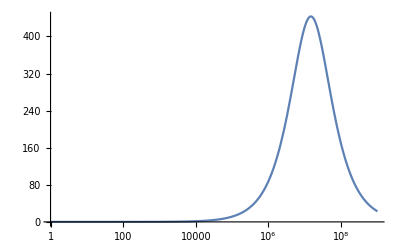

0.000767934

```mathematica
Q=3.416*10^-10;
R=1037.9;
n=0.9;
1/(R*Q)^(1/n)/2/Pi
res =Maximize[{(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2),w>0},w]
w/2/Pi/.res[[2]]
(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2)/.w->2621977.4532072237
LogLinearPlot[(Q w^n Sin[(n π)/2])/((1/R+Q w^n Cos[(n π)/2])^2+Q^2 w^(2 n) Sin[(n π)/2]^2),{w,1,10^9}, PlotRange->All]
```

```mathematica
ax.set_xlim(-20,1024)
```

```mathematica
2338028.0441190344/207500.1305668028
11990.297076661906/1729.086460240765
```

11.2676

6.93447